```mathematica
Needs["ErrorBarPlots`"]
GenerateListOfFileNames[prefix_,date_,runtimes_]:=Module[{j,fileNames},
fileNames={};
For[j=1,j≤Length[runtimes],j++,
AppendTo[fileNames,StringJoin[prefix,date,"_",ToString[runtimes[[j]]],".dat"]]
];
fileNames
];
GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
association=Append[association,rawFile[[k]][[1]]->rawFile[[k]][[2]]];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];
headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
SetAttributes[GetFileDataset,Listable];
SetAttributes[GetFileHeaderInfo,Listable];
SetAttributes[ImportFile,Listable];

FourierFit[list_,rev_]:=Module[{fit,function,dataPts,stepSize,dataPtsPerRev,angles,data(*,C0,C2,C4,S2,S4*)},

function[θ_]= C0+C2 Cos[2(θ+θo)]+C4 Cos[4(θ+θo)]+S2 Sin[2(θ+θo)]+S4 Sin[4(θ+θo)];
dataPts=Length[list];
dataPtsPerRev=dataPts/rev;
angles=Range[0,(2π*rev)-2π/dataPtsPerRev,2π/dataPtsPerRev];
data=Transpose[{list,angles}];
fit=NonlinearModelFit[data,function[θ],{{C0,1000},C2,C4,S2,S4,θo},θ]
];


DFT[list_,rev_]:=Module[{numItems,i,k,j,reconstructionCos,reconstructionSin,returnCos,errorsCos,returnSin,errorsSin,intensity},
returnCos={};
errorsCos={};
returnSin={};
errorsSin={};
reconstructionCos={};
reconstructionSin={};
numItems=Length[list];

For[j=0,j<numItems/2,j++,
AppendTo[returnCos,0];
AppendTo[returnSin,0];

];

For[i=1,i<=numItems,i++,
intensity=list[[i]];
For [k=0,k<numItems/2,k++,
If[k==0 ||k==(numItems/2-1),
returnCos[[k+1]]=N[returnCos[[k+1]]+1/numItems*intensity*Cos[2*π *k *rev* (i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+1/numItems*intensity*Sin[2*π *k *rev* (i-1)/numItems]];,
returnCos[[k+1]]=N[returnCos[[k+1]]+2/numItems*intensity*Cos[2*π *k* rev *(i-1)/numItems]];
returnSin[[k+1]]=N[returnSin[[k+1]]+2/numItems*intensity*Sin[2*π *k* rev *(i-1)/numItems]];
];
];
];
(*

For[j=0,j<numItems/2,j++,
AppendTo[errorsSin,0];
AppendTo[errorsCos,0];
For[i=1,i<=numItems,i++,
intensity=list[[i]];
AppendTo[reconstructionCos,0];
AppendTo[reconstructionSin,0];
reconstructionCos[[i]]=intensity/Cos[2*π*j*rev*(i)/numItems] ;
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]=intensity/Sin[2*π*1.0001*j*rev*(i)/numItems];];
For [k=0,k<numItems/2,k++,
If[k≠j,
reconstructionCos[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(i)/numItems] )/Cos[2*π*j*rev*(i)/numItems];
If[j==0,reconstructionSin[[i]]=0,reconstructionSin[[i]]-=(returnCos[[k+1]]*Cos[2*π*k*rev*(i)/numItems] +returnSin[[k+1]]*Sin[2*π*k*rev*(1)/numItems] )/Sin[2*π*1.0001*j*rev*(i)/numItems]];
];
];
errorsSin[[j+1]]+=Power[reconstructionSin[[i]]-returnSin[[j+1]],2];
errorsCos[[j+1]]+=Power[reconstructionCos[[i]]-returnCos[[j+1]],2];
];
errorsSin[[j+1]]=Sqrt[errorsSin[[j+1]]/numItems];
errorsCos[[j+1]]=Sqrt[errorsCos[[j+1]]/numItems];
];
*)
{{returnSin,errorsSin},{returnCos,errorsCos}}
];

StokesParametersFromFourierData[intensityArray_,rev_,alpha_,beta0_,delta_]:=
Module[{fc(*Fourrier Coefficients*),c0,c2,c4,s2,s4,stokes},
fc=DFT[intensityArray,rev];
stokes={0,0,0,0,0,0};
c0=fc[[2]][[1]][[1]];
c2=fc[[2]][[1]][[3]];
c4=fc[[2]][[1]][[5]];
s2=fc[[1]][[1]][[3]];
s4=fc[[1]][[1]][[5]];
stokes[[1]]=c0-(1+Cos[delta])/(1-Cos[delta])*(c4*Cos[4 alpha+4 beta0]+s4*Sin[4 alpha+4 beta0]);
stokes[[2]]=2/(1-Cos[delta])*(c4*Cos[2alpha + 4 beta0]+s4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[3]]=2/(1-Cos[delta])*(s4*Cos[2alpha + 4 beta0]-c4*Sin[2alpha + 4 beta0])/stokes[[1]];
stokes[[4]]=Sqrt[c2^2+s2^2]/(Sin[delta]^2 stokes[[1]]);
stokes[[5]]=c2/(Sin[delta]Sin[2 alpha + 4 beta0]stokes[[1]]);
stokes[[6]]=-s2/(Sin[delta]Cos[2 alpha + 4 beta0]stokes[[1]]);
stokes

];
StokesParametersFromPolFile[polFile_,alpha_,beta0_,delta_]:=
Module[{intensityArray,f,rev},
f=ImportFile[polFile];
intensityArray=Normal[f[[2]][All,"COUNT"]];
rev=f[[1]]["#REV:"];
StokesParametersFromFourierData[intensityArray,rev,alpha,beta0,delta]
];

GetLinearPolarizationFraction[fileName_]:=Module[{data,angle,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
intensity=fc[[2]][[1]];
linearPolarization=Sqrt[(fc[[2]][[3]])^2+(fc[[1]][[3]])^2];
linearPolarizationFraction=linearPolarization/intensity
];
SetAttributes[GetLinearPolarizationFraction,Listable];
GetAngle[fileName_]:=Module[{data,intensityArray,angleRAD,fc,intensity,linearPolarization,linearPolarizationFraction},
data=GetFileDataset[fileName];
intensityArray=Transpose[data][[2]];
fc=DFT[intensityArray,1] (*fc=fourier coefficients*);
.5*ArcTan[fc[[1]][[3]],fc[[2]][[3]]]
];
SetAttributes[GetAngle,Listable];

AverageDarkCountsRate[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/nCycles^2*dwell^2;
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];
DarkCountsRate[files_]:=Module[{i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
nDataPts=Length[Normal[files[[1]][[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell;
errorSum[[j]]+=counts[[j]]/nCycles^2*dwell^2;
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

AverageBackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=DarkCountsRate[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

BackgroundRateCurrentNorm[files_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=DarkCountsRate[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]];
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

AverageSignalRateCurrentNorm[files_,molyCountsRate_,darkCountsFiles_]:=Module[{darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,rev,j},
darkCountsRate=DarkCountsRate[darkCountsFiles];
nDataPts=Length[darkCountsRate[[1]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
For[i=1,i≤Length[files],i++,
counts=Normal[files[[i]][[2]][All,"COUNT"]];
current=Normal[files[[i]][[2]][All,"CURRENT"]];
dwell=files[[i]][[1]]["#DWELL(s):"];
rev=files[[i]][[1]]["#REV:"];
nCycles=Length[files];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/rev/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/rev/nCycles/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/rev/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*rev^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*rev^2*current[[j]]^2)-molyCountsRate[[2]][[j]]/(nCycles^2*rev^2);
];
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

SignalRateCurrentNormFromFiles[file_,molyCountFiles_,darkCountsFiles_]:=Module[{molyCountsRate,darkCountsRate,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
darkCountsRate=AverageDarkCountsRate[darkCountsFiles];
molyCountsRate=AverageBackgroundRateCurrentNorm[molyCountFiles,darkCountsFiles];
SignalRateCurrentNormFromRates[file,molyCountFiles,darkCountsFiles]
];

SignalRateCurrentNormFromRates[fileName_,molyCountsRate_,darkCountsRate_]:=Module[{file,i,sum,counts,dwell,current,nCycles,errorSum, error,nDataPts,j},
file=ImportFile[fileName];
nDataPts=Length[Normal[file[[2]][All,"COUNT"]]];
sum={};errorSum={};
For[j=1,j≤ nDataPts,j++,
sum=AppendTo[sum,0];
errorSum=AppendTo[errorSum,0];
];
counts=Normal[file[[2]][All,"COUNT"]];
current=Normal[file[[2]][All,"CURRENT"]];
dwell=file[[1]]["#DWELL(s):"];
nCycles=file[[1]]["#REV:"];
For[j=1,j≤nDataPts,j++,
sum[[j]]+=counts[[j]]/nCycles/dwell/Abs[current[[j]]]-darkCountsRate[[1]][[j]]/nCycles/Abs[current[[j]]]-molyCountsRate[[1]][[j]]/nCycles;
errorSum[[j]]+=counts[[j]]/(nCycles^2*dwell^2*current[[j]]^2)-darkCountsRate[[2]][[j]]/(nCycles^2*current[[j]]^2)-molyCountsRate[[2]][[j]]/(nCycles^2);
];
For[j=1,j≤ nDataPts,j++,
errorSum[[j]]=Sqrt[errorSum[[j]]];
];
{sum,errorSum}
];

CalculateOneFileStokes[polFileName_,molyCountRate_,darkCountRate_,alpha_,beta_,delta_]:=Module[{signal,stokes,file,rev},
file=ImportFile[polFileName];
rev=file[[1]]["#REV:"];
signal=SignalRateCurrentNormFromRates[polFileName,molyCountRate,darkCountRate];
StokesParametersFromFourierData[signal[[1]],rev,alpha,beta,delta]
];

CalculateAverageStokes[polFileNames_,molyCountRate_,darkCountRate_,alpha_,beta_,delta_]:=Module[{signal,stokes,stokesStdDev,file,rev,j,i,stokesValues,transposedValues},
stokes={0,0,0,0,0,0};
stokesStdDev={0,0,0,0,0,0};
stokesValues={};
For[j=1,j≤Length[polFileNames],j++,
stokes=CalculateOneFileStokes[polFileNames[[j]],molyCountRate,darkCountRate,alpha,beta,delta];
AppendTo[stokesValues,stokes]
];
transposedValues=Transpose[stokesValues];
For[i=1,i≤Length[stokes],i++,
stokes[[i]]=Mean[transposedValues[[i]]];
stokesStdDev[[i]]=StandardDeviation[transposedValues[[i]]]/Sqrt[Length[transposedValues]];
];
{stokes,stokesStdDev}
]
```

```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-10-20"}];
dropBoxfolder=FileNameJoin[{"C:","Users","kahrendsen2","Dropbox"}];
dataFolder=FileNameJoin[{"00School","research","DataRuns"}];
folder=FileNameJoin[{dropBoxfolder,dataFolder}];
SetDirectory[folder];
FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,NewFile2.tsv,NewFile.tsv,pumpPower.png}

```mathematica
SetDirectory[FileNameJoin[{folder,"17-10-26_24and30eVRuns"}]];
names=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]];
darkFileNames=Take[names,2]
darkFiles=ImportFile[darkFileNames]; (* A "File" here means a list consisting of two elements. The first element is a list of associations containing information pertinent to all of the datapoints, the "header." The second element is the dataset.*)
darkCounts=N[DarkCountsRate[darkFiles]](*DarkCountsRate takes as an argument a list of "files" as defined above, and returns two lists. The first list is the average dark count at each polarimeter position. The second list is the standard deviation of that countRate, as per Clayburn's thesis.*)
```

{POL2017-10-26_080223.dat,POL2017-10-26_080342.dat}

{{45.,33.5,40.5,54.5,43.,46.,47.5,51.5,52.5,35.5,49.,51.,38.,48.5,41.5,46.5,50.,46.,46.5,42.5,52.,46.,52.,49.5,48.,38.5,35.5,47.,39.,43.5,37.,43.5,44.,44.5,54.5,66.,38.,43.,50.5,49.5,43.,39.,51.,42.5,40.5,36.,44.5,43.5,48.,44.5,40.5,39.5,50.,49.,37.,50.,42.5,35.,46.,47.5},{4.74342,4.09268,4.5,5.22015,4.63681,4.79583,4.8734,5.07445,5.12348,4.21307,4.94975,5.04975,4.3589,4.92443,4.55522,4.82183,5.,4.79583,4.82183,4.60977,5.09902,4.79583,5.09902,4.97494,4.89898,4.38748,4.21307,4.84768,4.41588,4.66369,4.30116,4.66369,4.69042,4.71699,5.22015,5.74456,4.3589,4.63681,5.02494,4.97494,4.63681,4.41588,5.04975,4.60977,4.5,4.24264,4.71699,4.66369,4.89898,4.71699,4.5,4.4441,5.,4.94975,4.30116,5.,4.60977,4.1833,4.79583,4.8734}}

```mathematica
SetDirectory[FileNameJoin[{folder,"17-11-06_UnpolarizedRuns2"}]];
names=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]];

runs=10;
energies={30,27,24,23,22,16};
energyXmolyFileNames={};
energyXsignalFileNames={};
For[i=1,i≤Length[energies],i++,
molyFileNames=Take[names,{(i+Length[energies]*runs),(2*Length[energies]*runs),(Length[energies])}];
signalFileNames=Take[names,{i+0,Length[energies]*runs,Length[energies]}];
AppendTo[energyXmolyFileNames,molyFileNames];
AppendTo[energyXsignalFileNames,signalFileNames];
];

energyXmolyFileNames
```

{{POL2017-11-08_092806.dat,POL2017-11-08_100706.dat,POL2017-11-08_104606.dat,POL2017-11-08_112507.dat,POL2017-11-08_120407.dat,POL2017-11-08_124310.dat,POL2017-11-08_132210.dat,POL2017-11-08_140111.dat,POL2017-11-08_144011.dat,POL2017-11-08_151912.dat},{POL2017-11-08_093436.dat,POL2017-11-08_101336.dat,POL2017-11-08_105237.dat,POL2017-11-08_113137.dat,POL2017-11-08_121037.dat,POL2017-11-08_124940.dat,POL2017-11-08_132840.dat,POL2017-11-08_140741.dat,POL2017-11-08_144641.dat,POL2017-11-08_152542.dat},{POL2017-11-08_094106.dat,POL2017-11-08_102006.dat,POL2017-11-08_105907.dat,POL2017-11-08_113807.dat,POL2017-11-08_121707.dat,POL2017-11-08_125610.dat,POL2017-11-08_133511.dat,POL2017-11-08_141411.dat,POL2017-11-08_145311.dat,POL2017-11-08_153212.dat},{POL2017-11-08_094736.dat,POL2017-11-08_102636.dat,POL2017-11-08_110537.dat,POL2017-11-08_114437.dat,POL2017-11-08_122338.dat,POL2017-11-08_130240.dat,POL2017-11-08_134141.dat,POL2017-11-08_142041.dat,POL2017-11-08_145941.dat,POL2017-11-08_153842.dat},{POL2017-11-08_095406.dat,POL2017-11-08_103306.dat,POL2017-11-08_111207.dat,POL2017-11-08_115107.dat,POL2017-11-08_123008.dat,POL2017-11-08_130910.dat,POL2017-11-08_134811.dat,POL2017-11-08_142711.dat,POL2017-11-08_150611.dat,POL2017-11-08_154512.dat},{POL2017-11-08_100036.dat,POL2017-11-08_103936.dat,POL2017-11-08_111837.dat,POL2017-11-08_115737.dat,POL2017-11-08_123638.dat,POL2017-11-08_131540.dat,POL2017-11-08_135441.dat,POL2017-11-08_143341.dat,POL2017-11-08_151241.dat,POL2017-11-08_155142.dat}}

```mathematica
averagedMolyDarkSubtracted={};

For[j=1,j≤Length[energyXmolyFileNames],j++,
files=ImportFile[energyXmolyFileNames[[j]]];
averageMolyDarkSubtracted=N[AverageBackgroundRateCurrentNorm[files,darkFiles]];
AppendTo[averagedMolyDarkSubtracted,averageMolyDarkSubtracted];
];
```

```mathematica
averagedSignalBackgroundSubtracted={};


For[j=1,j≤Length[energyXsignalFileNames],j++,
files=ImportFile[energyXsignalFileNames[[j]]];
averageSignalBackgroundSubtracted=N[AverageSignalRateCurrentNorm[files,averagedMolyDarkSubtracted[[j]],darkFiles]];
AppendTo[averagedSignalBackgroundSubtracted,averageSignalBackgroundSubtracted];
];
averagedSignalBackgroundSubtracted
```

{{{763.025,766.157,762.779,749.146,735.413,733.159,733.511,724.875,755.391,760.962,764.677,791.294,791.105,789.431,763.803,769.609,753.21,743.748,739.732,738.595,726.925,717.288,733.008,751.235,755.242,763.801,777.707,774.051,780.653,775.881,776.368,770.762,753.773,737.798,735.681,721.45,736.484,740.141,746.265,752.712,762.444,777.978,777.503,781.904,777.99,771.224,760.726,744.427,739.846,727.492,721.952,726.318,729.387,748.446,762.356,759.203,773.913,785.977,787.387,773.909},{4.78097,4.80141,4.79324,4.73312,4.70941,4.70977,4.70545,4.67301,4.75343,4.78121,4.7768,4.84224,4.85629,4.85785,4.79721,4.80409,4.75589,4.74308,4.72788,4.73467,4.69125,4.67791,4.69958,4.75084,4.76456,4.7935,4.83007,4.81204,4.84283,4.81986,4.84349,4.81764,4.78167,4.72635,4.70692,4.65393,4.7162,4.73245,4.73971,4.74631,4.77952,4.82682,4.80893,4.81705,4.82256,4.80841,4.75863,4.72045,4.71269,4.68212,4.66624,4.68585,4.66798,4.71883,4.76979,4.75294,4.80209,4.8472,4.84217,4.80858}},{{683.683,688.303,666.347,671.568,658.566,663.764,653.763,657.964,658.237,672.227,682.181,684.153,695.482,694.632,688.027,671.747,669.112,661.089,649.408,651.266,652.576,648.463,653.756,656.422,666.044,675.181,686.966,696.318,705.426,696.367,680.34,677.721,669.215,667.497,654.162,645.753,653.343,649.806,669.949,680.038,676.158,685.78,689.358,702.069,691.917,688.331,679.769,660.448,664.56,656.23,642.036,657.346,657.762,660.238,664.417,683.735,691.293,693.858,690.271,684.352},{4.53126,4.55394,4.48213,4.49163,4.46801,4.47627,4.44878,4.45734,4.44995,4.51096,4.51091,4.5066,4.56019,4.54171,4.53927,4.4824,4.47894,4.46217,4.42223,4.43532,4.42841,4.42974,4.42644,4.43969,4.46856,4.49583,4.53678,4.55187,4.58553,4.54095,4.51814,4.50554,4.47768,4.47659,4.44116,4.39444,4.44441,4.42926,4.46511,4.48925,4.47315,4.52095,4.5013,4.54814,4.53206,4.52399,4.49871,4.44482,4.45907,4.4368,4.40227,4.43948,4.43322,4.44016,4.45772,4.4846,4.52564,4.53659,4.52323,4.50557}},{{173.762,173.056,170.1,158.822,162.719,163.125,162.317,166.929,169.309,176.167,173.469,172.819,176.873,177.585,170.004,167.683,165.863,172.648,156.556,156.921,162.535,166.714,166.73,168.144,160.627,179.56,173.652,174.314,173.09,168.285,172.757,169.478,164.794,159.391,156.438,150.655,159.747,165.032,159.618,167.471,170.052,178.553,165.47,173.515,174.037,172.65,176.69,158.866,164.067,158.284,159.065,158.31,159.737,165.06,170.038,170.804,175.595,175.589,173.652,171.659},{2.44892,2.48,2.45746,2.38848,2.42166,2.4193,2.4113,2.41734,2.42172,2.49657,2.44926,2.4294,2.48705,2.4717,2.45081,2.42324,2.41686,2.46521,2.39813,2.41656,2.41958,2.43667,2.42374,2.43498,2.40277,2.49927,2.46496,2.43872,2.46816,2.44843,2.47629,2.45392,2.43015,2.41208,2.37659,2.34187,2.42645,2.42482,2.39454,2.44652,2.47722,2.5137,2.42299,2.46626,2.49166,2.50294,2.50239,2.43276,2.44065,2.4157,2.4437,2.43732,2.42051,2.42944,2.47694,2.4468,2.50747,2.49701,2.46591,2.4614}},{{-24.8963,-21.3381,-20.9201,-32.7152,-26.8988,-34.7224,-34.7247,-31.3761,-31.8726,-28.7655,-30.2042,-29.8068,-24.2607,-27.292,-26.4215,-30.2362,-33.894,-27.3659,-34.0324,-30.5975,-38.4451,-31.4963,-36.1993,-31.6234,-30.8785,-25.0826,-22.0264,-25.3302,-24.3507,-25.5873,-31.4535,-26.6696,-32.3713,-33.6501,-34.4979,-40.789,-36.3891,-36.2082,-36.8659,-29.5596,-26.3222,-26.196,-26.7974,-25.8203,-27.855,-28.1405,-29.5196,-27.8869,-32.2048,-33.8814,-33.5397,-32.8108,-34.1301,-30.9264,-28.9279,-30.4577,-27.2934,-28.0388,-29.4261,-27.3022},{0.7293,0.873135,0.815674,0.587858,0.755513,0.605593,0.587736,0.539899,0.526304,0.697084,0.565274,0.512399,0.686032,0.609297,0.660306,0.563967,0.467032,0.639267,0.532425,0.65296,0.43987,0.688145,0.488391,0.538355,0.561497,0.670338,0.738466,0.571436,0.70435,0.625618,0.655985,0.661541,0.635053,0.67411,0.493202,0.236768,0.645821,0.600454,0.463257,0.547457,0.624471,0.698447,0.478478,0.638678,0.641902,0.685283,0.605886,0.658386,0.588434,0.628016,0.57547,0.654562,0.47663,0.537132,0.679644,0.514207,0.601357,0.677297,0.542395,0.587221}},{{-47.5409,-45.8915,-46.3135,-55.8598,-52.0828,-52.5605,-48.3242,-51.3943,-49.1295,-42.9854,-46.9555,-44.33,-37.1645,-44.8899,-45.566,-44.5189,-48.4934,-46.619,-47.4707,-54.1462,-50.7275,-48.086,-47.3365,-49.2074,-45.7374,-46.13,-42.6954,-41.9015,-42.107,-45.6376,-46.4867,-44.8049,-49.9653,-48.9712,-58.9378,-54.2503,-51.0102,-51.6991,-46.5266,-46.5606,-42.0237,-41.598,-44.7919,-45.6231,-47.2781,-51.0068,-47.6983,-45.1009,-46.6803,-49.5402,-47.9258,-52.3433,-48.3129,-49.8384,-45.6656,-44.3422,-47.3966,-46.1197,-40.2384,-46.1168},{0.+0.416633 ⅈ,0.13862,0.+0.27312 ⅈ,0.+0.580639 ⅈ,0.+0.361471 ⅈ,0.+0.482375 ⅈ,0.+0.427271 ⅈ,0.+0.523878 ⅈ,0.+0.513346 ⅈ,0.+0.182748 ⅈ,0.+0.502418 ⅈ,0.+0.529167 ⅈ,0.0670533,0.+0.459083 ⅈ,0.+0.4012 ⅈ,0.+0.410319 ⅈ,0.+0.496401 ⅈ,0.+0.452358 ⅈ,0.+0.407183 ⅈ,0.+0.303032 ⅈ,0.+0.518276 ⅈ,0.+0.34492 ⅈ,0.+0.465931 ⅈ,0.+0.461142 ⅈ,0.+0.390992 ⅈ,0.+0.245004 ⅈ,0.+0.208617 ⅈ,0.+0.36139 ⅈ,0.+0.248837 ⅈ,0.+0.395606 ⅈ,0.+0.210078 ⅈ,0.+0.364556 ⅈ,0.+0.406736 ⅈ,0.+0.30413 ⅈ,0.+0.603698 ⅈ,0.+0.67338 ⅈ,0.+0.264186 ⅈ,0.+0.424609 ⅈ,0.+0.538933 ⅈ,0.+0.463497 ⅈ,0.+0.325698 ⅈ,0.+0.331741 ⅈ,0.+0.49252 ⅈ,0.+0.453622 ⅈ,0.+0.328596 ⅈ,0.+0.315722 ⅈ,0.+0.406368 ⅈ,0.+0.285347 ⅈ,0.+0.459888 ⅈ,0.+0.318141 ⅈ,0.+0.307505 ⅈ,0.+0.324579 ⅈ,0.+0.427483 ⅈ,0.+0.492759 ⅈ,0.+0.205234 ⅈ,0.+0.545184 ⅈ,0.+0.491775 ⅈ,0.+0.216515 ⅈ,0.+0.322107 ⅈ,0.+0.479136 ⅈ}},{{-47.83,-43.8741,-50.9571,-55.8158,-57.7711,-54.9502,-53.9598,-53.1806,-55.7234,-46.8219,-43.6529,-49.1539,-45.9948,-48.8271,-47.1694,-47.7137,-51.5483,-54.224,-56.5168,-55.4381,-53.8636,-54.5544,-54.1896,-49.5815,-51.0822,-47.5183,-45.7162,-50.2208,-48.0765,-48.9411,-53.9622,-52.4087,-54.7286,-53.4579,-54.9917,-60.7549,-57.9071,-56.8345,-53.0756,-49.0408,-48.3522,-48.2412,-49.7464,-49.2555,-44.6415,-46.2991,-51.0016,-51.4534,-57.6686,-52.7585,-53.5849,-53.6451,-54.2224,-53.0808,-50.4114,-46.5125,-46.6259,-47.5536,-51.1024,-48.9676},{0.+0.47307 ⅈ,0.0855143,0.+0.356588 ⅈ,0.+0.581386 ⅈ,0.+0.453032 ⅈ,0.+0.475036 ⅈ,0.+0.520356 ⅈ,0.+0.52269 ⅈ,0.+0.615013 ⅈ,0.+0.284639 ⅈ,0.+0.496703 ⅈ,0.+0.504077 ⅈ,0.+0.293459 ⅈ,0.+0.517651 ⅈ,0.+0.377533 ⅈ,0.+0.505775 ⅈ,0.+0.568816 ⅈ,0.+0.495512 ⅈ,0.+0.55742 ⅈ,0.+0.403214 ⅈ,0.+0.485442 ⅈ,0.+0.473813 ⅈ,0.+0.567151 ⅈ,0.+0.531561 ⅈ,0.+0.55567 ⅈ,0.+0.389189 ⅈ,0.+0.133731 ⅈ,0.+0.538361 ⅈ,0.+0.374128 ⅈ,0.+0.511889 ⅈ,0.+0.298709 ⅈ,0.+0.439206 ⅈ,0.+0.54535 ⅈ,0.+0.4298 ⅈ,0.+0.570974 ⅈ,0.+0.714855 ⅈ,0.+0.362814 ⅈ,0.+0.533044 ⅈ,0.+0.575207 ⅈ,0.+0.517628 ⅈ,0.+0.40343 ⅈ,0.+0.400675 ⅈ,0.+0.546438 ⅈ,0.+0.519232 ⅈ,0.+0.341056 ⅈ,0.+0.144654 ⅈ,0.+0.401336 ⅈ,0.+0.318781 ⅈ,0.+0.515414 ⅈ,0.+0.35784 ⅈ,0.+0.321423 ⅈ,0.+0.404775 ⅈ,0.+0.542809 ⅈ,0.+0.523432 ⅈ,0.+0.314873 ⅈ,0.+0.498022 ⅈ,0.+0.43448 ⅈ,0.+0.281639 ⅈ,0.+0.562195 ⅈ,0.+0.484191 ⅈ}}}

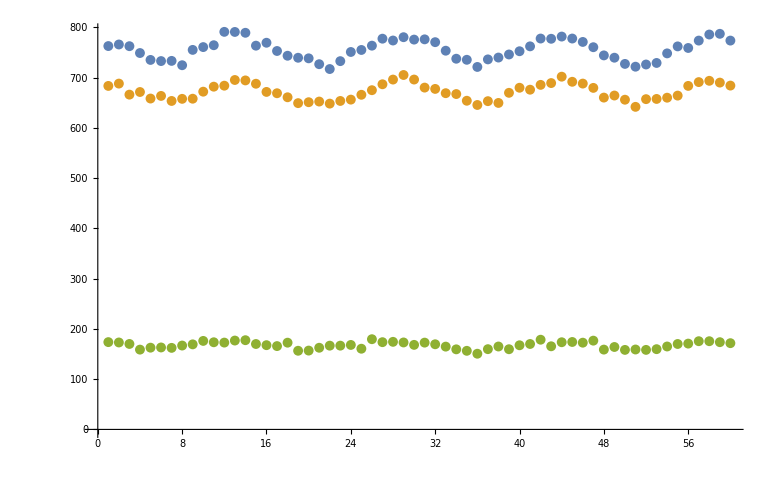

```mathematica
ListPlot[{averagedSignalBackgroundSubtracted[[1]][[1]],averagedSignalBackgroundSubtracted[[2]][[1]],averagedSignalBackgroundSubtracted[[3]][[1]]}]
```

```mathematica
alpha=3.2*π/180;
beta=-6.95*π/180;
deltaAB=alpha-beta;
delta=90*π/180;


stokesAverages={};
stokesStdMs={};
energy=energies

For[j=1,j≤Length[energy],j++,
runs={};
signal=energyXsignalFileNames[[j]];
molyCounts=averagedMolyDarkSubtracted[[j]];

For[i=1,i≤Length[signal],i++,
subtracted=SignalRateCurrentNormFromRates[signal[[i]],molyCounts,darkCounts];
AppendTo[runs,subtracted];
];

stokesData={};
For[i=1,i≤Length[signal],i++,
stokes=StokesParametersFromFourierData[runs[[i]][[1]],1,alpha,beta,delta];
Print[stokes];
AppendTo[stokesData,stokes];
];

p1Avg=Mean[Transpose[stokesData][[2]]];
p2Avg=Mean[Transpose[stokesData][[3]]];
p3Avg=Mean[Transpose[stokesData][[4]]];
p3Avg2=Mean[Transpose[stokesData][[5]]];

p1Std=StandardDeviation[Transpose[stokesData][[2]]];
p2Std=StandardDeviation[Transpose[stokesData][[3]]];
p3Std=StandardDeviation[Transpose[stokesData][[4]]];
p3Std2=StandardDeviation[Transpose[stokesData][[5]]];
stokesAverage={p1Avg,p2Avg,p3Avg,p3Avg2};
stokesStdM={p1Std,p2Std,p3Std,p3Std2}/Sqrt[10];
AppendTo[stokesAverages,stokesAverage];
AppendTo[stokesStdMs,stokesStdM];
]

stokesParam={};
energyStokesWError={};
For[j=1,j≤Length[stokesAverage],j++,(*The Stokes parameters loop over # of stokes*)
stokesIndex=j;
px={};
For[i=1,i≤Length[energy],i++,(* The energy Loop, over number of energies*)
AppendTo[px,stokesAverages[[i]][[j]]];
];
AppendTo[stokesParam,px];
errorBars={};
For[i=1,i≤Length[energy],i++,(* The energy Loop, over number of energies*)
AppendTo[errorBars,ErrorBar[stokesStdMs[[i]][[j]]]];
];
(*errorBars={ErrorBar[stokesStdMs[[1]][[j]]],ErrorBar[stokesStdMs[[2]][[j]]],ErrorBar[stokesStdMs[[3]][[j]]]};*)
energyVsPx={};
For[i=1,i≤Length[energy],i++,(* The energy Loop, over number of energies*)
AppendTo[energyVsPx,{Transpose[{energy,stokesParam[[j]]}][[i]],errorBars[[i]]}];
];
AppendTo[energyStokesWError,energyVsPx];
];
```

{30,27,24,23,22,16}

{792.577,0.0375655,-0.0266362,0.0104628,-0.0120278,-0.0102012}

{717.769,0.0669684,-0.0390343,0.00538026,-0.0121029,-0.00330092}

{726.344,0.0677677,-0.0531244,0.00184743,0.00448935,-0.000917522}

{728.386,0.0729227,-0.0435746,0.00503219,-0.00180536,-0.00535831}

{731.175,0.0651892,-0.0423895,0.0126579,-0.0286136,-0.00768668}

{731.384,0.0639273,-0.0321212,0.00290379,0.00687161,-0.00157322}

{734.399,0.0492408,-0.0549998,0.00143203,-0.00024874,-0.00153498}

{721.731,0.0737416,-0.040743,0.00284387,-0.00642663,0.00172815}

{733.705,0.0574455,-0.0361957,0.00582008,-0.0127912,-0.00373464}

{732.471,0.0626352,-0.0392562,0.00394767,-0.00225844,-0.00414659}

{706.698,0.0432902,-0.0263644,0.00420906,-0.0103475,-0.00199821}

{633.553,0.0702738,-0.0348987,0.00734594,-0.0198574,0.0013003}

{651.157,0.0504382,-0.0331183,0.0124833,-0.0180203,-0.011397}

{649.472,0.0555872,-0.0259161,0.0049074,0.00773078,0.00431305}

{649.237,0.0706932,-0.051394,0.00722206,0.0186437,-0.00260488}

{653.934,0.050246,-0.0398538,0.00741701,0.00292547,-0.00788331}

{649.435,0.0727215,-0.0455259,0.00871444,-0.0237728,0.000899249}

{649.17,0.0578209,-0.0317409,0.0107459,-0.0281079,-0.00344549}

{655.862,0.0494701,-0.0147481,0.00633285,-0.0161464,-0.00249494}

{651.761,0.0434722,-0.0308153,0.00954836,-0.0064784,-0.00993618}

{216.737,0.0461248,-0.0327136,0.00615451,0.0166682,0.00101286}

{152.375,0.0828129,-0.061516,0.0116026,-0.0239399,0.00820206}

{156.816,0.0581933,-0.0751022,0.00418806,0.00814515,-0.0031693}

{158.914,0.0653134,-0.0807218,0.0193207,-0.0185417,-0.0194375}

{155.88,0.0630898,-0.0530414,0.00574261,0.015241,0.00153849}

{153.724,0.0874691,-0.104568,0.0154906,-0.0303857,0.0116194}

{155.687,0.0872863,-0.0862046,0.00901461,-0.0126857,-0.00830832}

{158.858,0.0753113,-0.0537792,0.0140323,-0.0351156,-0.00614521}

{161.683,0.0403592,-0.0435891,0.0205947,0.0428512,0.014397}

{156.525,0.0830315,-0.0672565,0.00609173,0.0163339,-0.00135399}

{-36.4531,-0.420059,-0.407912,-0.286595,0.763571,0.0721599}

{-36.5543,-0.169663,0.0990302,-0.0457635,0.014687,-0.0488141}

{-35.4916,-0.252438,0.138516,-0.0327524,0.047597,-0.0298251}

{-32.3055,-0.236554,0.214682,-0.0394907,-0.0878999,-0.0247466}

{-33.1828,-0.17523,0.206534,-0.0219419,-0.0541709,-0.0102326}

{-33.7321,-0.163001,0.172577,-0.0317463,0.00197094,-0.0340884}

{-33.6409,-0.206871,0.169522,-0.0361683,-0.0868776,-0.0187046}

{-33.033,-0.288666,0.163772,-0.051995,-0.141042,0.00796731}

{-31.658,-0.192421,0.156319,-0.0174274,-0.0181034,0.0173213}

{-30.9687,-0.216019,0.193538,-0.0437184,0.0685942,-0.0384995}

{-52.3038,-0.0919489,0.0888984,-0.0228025,-0.0599752,0.00688255}

{-51.8581,-0.125139,0.070223,-0.01578,-0.0363851,-0.00916127}

{-50.5194,-0.0925952,0.179044,-0.0207702,-0.0123831,-0.021774}

{-51.0298,-0.0966564,0.114938,-0.00942814,0.014176,0.00846629}

{-49.6668,-0.13307,0.109342,-0.0311013,0.0149733,-0.0328849}

{-51.4487,-0.122875,0.0792156,-0.0171776,-0.0455652,0.00463906}

{-46.9932,-0.0888483,0.165517,-0.0124956,-0.030328,-0.00623348}

{-46.234,-0.115055,0.115384,-0.0210182,-0.0574725,-0.00152185}

{-50.3145,-0.139916,0.137781,-0.0540724,-0.0408615,-0.0558251}

{-46.2379,-0.0637561,0.151928,-0.0195595,-0.0461262,-0.0107035}

{-58.8729,-0.156946,0.0847762,-0.0141157,-0.0368058,0.00466909}

{-53.7064,-0.0744042,0.15632,-0.0349027,-0.0177783,-0.0368341}

{-56.0494,-0.170556,0.0633633,-0.00922068,-0.0183815,-0.00679604}

{-53.4669,-0.131381,0.063797,-0.00222588,0.00595956,0.000510655}

{-55.3822,-0.0813894,0.114369,-0.0145991,0.0352601,-0.00741094}

{-55.9699,-0.111105,0.164616,-0.0136936,-0.0265995,-0.0103754}

{-52.6027,-0.0789798,0.0956244,-0.0238972,-0.0605576,0.00977553}

{-53.3582,-0.127878,0.12176,-0.0101797,-0.0255222,0.00441606}

{-48.7939,-0.0791026,0.173666,-0.00195201,0.000404046,-0.00209057}

{-52.0275,-0.128106,0.118794,-0.042785,-0.0854212,-0.0314808}

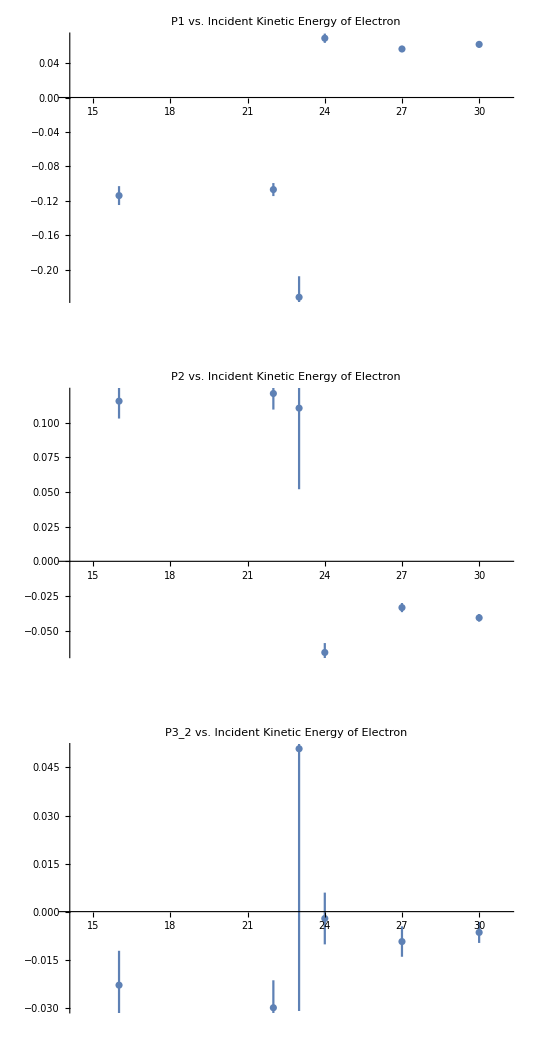

```mathematica
p1=ErrorListPlot[energyStokesWError[[1]],PlotLabel->"P1 vs. Incident Kinetic Energy of Electron",PlotRange->{{14,31},All}];
p2=ErrorListPlot[energyStokesWError[[2]],PlotLabel->"P2 vs. Incident Kinetic Energy of Electron",PlotRange->{{14,31},All}];
p3=ErrorListPlot[energyStokesWError[[3]],PlotLabel->"P3 vs. Incident Kinetic Energy of Electron",PlotRange->{{14,31},All}];
p3pt2=ErrorListPlot[energyStokesWError[[4]],PlotLabel->"P3_2 vs. Incident Kinetic Energy of Electron",PlotRange->{{14,31},All}];
GraphicsGrid[{{p1},{p2},{p3pt2}}]
```

## Finding QWP Position:

```mathematica
SetDirectory[FileNameJoin[{folder,"17-11-04_MoreUnpolarizedRuns"}]];
names=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]];
fileName=names[[1]];
file=ImportFile[fileName];
dataset=file[[2]];
fourierData=Normal[dataset[All,"COUNT"]];
StokesParametersFromPolFile[fileName,20.4*π/180,1.105,delta]
```

{134785.,0.0478829,-0.00045076,0.00153063,-0.00157554,0.00128148}

```mathematica
20.4*π/180
```

0.356047